```mathematica
m1 = 40;
m2 = 20;
μ = m2/m1;
wz = 0.54078;
wip = √((1+μ-√(1-μ+μ^2))/μ)wz;
wop = √((1+μ+√(1-μ+μ^2))/μ)wz;
wip
wop
```

0.608936

1.17637

```mathematica
178.11+176.61
```

```mathematica
354.72/2
```

177.36

0.735

1.27306

```mathematica
m1 = 9;
m2 = 25;
μ = m2/m1;
wz = 0.735;
wip = √((1+μ-√(1-μ+μ^2))/μ)wz;
wop = √((1+μ+√(1-μ+μ^2))/μ)wz;
wip
wop
```

0.51067

1.09938

```mathematica
(6.626*10^-34*3*10^8)/(1.38*10^-23*300)
```

0.0000480145

```mathematica
1.38*10^-23*300/(6.626*10^-34)
```

6.24811×10^12

```mathematica
LaguerreL[5,0.01]
```

0.950498

```mathematica
(196.835+197.435)/2
```

197.135

```mathematica
√((86.8+89.2)/(24.6+41.0))*197.135
```

322.9

```mathematica
√(267/87.5)*338
```

590.43

```mathematica
√(((506+456)/2)/267)*598
```

598 √(481/267)

```mathematica
N[598 √(481/267)]
```

802.635

```mathematica
(24.6+41.0)/2
```

32.8

```mathematica
(86.8 + 89.2)/2
```

88.

```mathematica
(233.6 + 214.7)/2
```

224.15

```mathematica
(278.8 + 256.1)/2
```

267.45

```mathematica
freq={197.235,338,549,598}
```

{197.235,338,549,598}

```mathematica
voltage={32.8,88.,224.14999999999998,267.45000000000005}
```

{32.8,88.,224.15,267.45}

```mathematica
Plot[freq,voltage]
```

Plot::pllim: Range specification voltage is not of the form {x, xmin, xmax}.

Plot[freq,voltage]

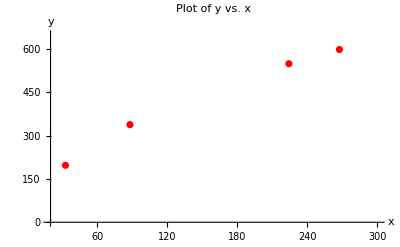

```mathematica
freq={197.235,338,549,598};voltage={32.8,88.,224.14999999999998,267.45000000000005};
ListPlot[Transpose[{voltage,freq}],AxesLabel->{"x","y"},PlotLabel->"Plot of y vs. x",PlotRange->{{20,300},{0,650}},BaseStyle->{FontFamily->"Helvetica",FontSize->12},PlotStyle->Red]
```

General::ivar: 1 is not a valid variable.

General::ivar: 1. is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

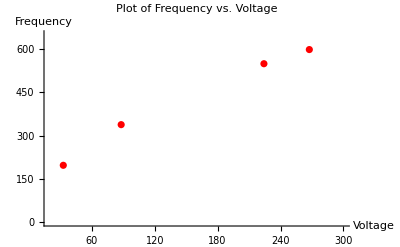

```mathematica
freq={197.235,338,549,598};
voltage={32.8,88.,224.14999999999998,267.45000000000005};

data=Transpose[{voltage,freq}];
model=NonlinearModelFit[data,C*Sqrt[x],C,x];

Show[ListPlot[data,PlotStyle->Red],Plot[model[x],{x,20,300}],AxesLabel->{"Voltage","Frequency"},PlotLabel->"Plot of Frequency vs. Voltage",PlotRange->{{20,300},{0,650}},BaseStyle->{FontFamily->"Helvetica",FontSize->12}]
```

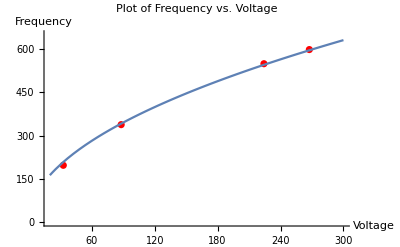

```mathematica
freq={197.235,338,549,598};
voltage={32.8,88.,224.14999999999998,267.45000000000005};

data=Transpose[{voltage,freq}];
model=NonlinearModelFit[data,C*Sqrt[v],C,v];

Show[ListPlot[data,PlotStyle->Red],Plot[model[x],{x,20,300}],AxesLabel->{"Voltage","Frequency"},PlotLabel->"Plot of Frequency vs. Voltage",PlotRange->{{20,300},{0,650}},BaseStyle->{FontFamily->"Helvetica",FontSize->12}]
```

```mathematica
C
```

C

| Estimate | Standard Error | t-Statistic | P-Value
C | 36.4131 | 0.256924 | 141.727 | 1.48662×10^-8

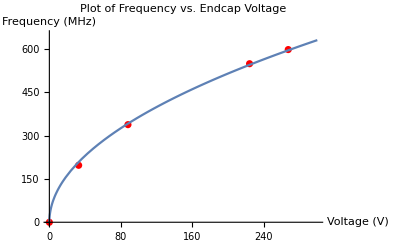

```mathematica
freq={0,197.235,338,549,598};
voltage={0,32.8,88.,224.14999999999998,267.45000000000005};

data=Transpose[{voltage,freq}];
model=NonlinearModelFit[data,C*Sqrt[v],C,v];
parameterTable=model["ParameterTable"]

Show[ListPlot[data,PlotStyle->Red],Plot[model[x],{x,0,300}],AxesLabel->{"Voltage (V)","Frequency (MHz)"},PlotLabel->"Plot of Frequency vs. Endcap Voltage\n",PlotRange->{{0,300},{0,650}},BaseStyle->{FontFamily->"Helvetica",FontSize->12}]
```

```mathematica
36.41308439480629*√800
```

1029.92

| Estimate | Standard Error | t-Statistic | P-Value
C | 36.4131 | 0.256924 | 141.727 | 1.48662×10^-8

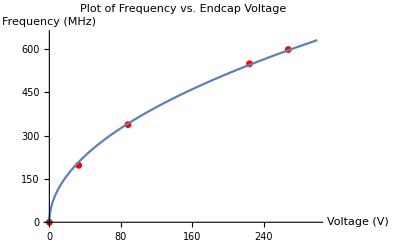

```mathematica
freq={0,197.235,338,549,598};
voltage={0,32.8,88.,224.14999999999998,267.45000000000005};

data=Transpose[{voltage,freq}];
model=NonlinearModelFit[data,C*Sqrt[v],C,v];
parameterTable=model["ParameterTable"]

Show[ListPlot[data,PlotStyle->Red,PlotMarkers->{Automatic,7}],Plot[model[x],{x,0,300}],AxesLabel->{"Voltage (V)","Frequency (MHz)"},PlotLabel->"Plot of Frequency vs. Endcap Voltage\n",PlotRange->{{0,300},{0,650}},BaseStyle->{FontFamily->"Helvetica",FontSize->12}]
```

```mathematica
5.1/322.9
```

0.0157944

```mathematica
9/540
```

1/60

```mathematica
N[1/60]
```

0.0166667

```mathematica
8/590
```

4/295

```mathematica
N[4/295]
```

0.0135593